```mathematica
Quit[];
```

```mathematica
(*HEALTHY state*)
Wss=0;
Wgs=1.12;
Wsg=19;
Wgg=6.6;
Wcs=2.42;
Wxg=15.1;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS= 6;(*tau_s=tau_g*)
```

```mathematica
(*coefficients and function in rescaled system*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*region spanned by alpha and beta, by varying Wgs and Wsg*)
p1=ParametricPlot[{alpha[Wgs,Wsg],beta[Wgs,Wsg]},{Wsg,0,30},{Wgs,0,20},PlotRange->All,PlotStyle->Red,Axes->False,Frame->True,PlotPoints->100]
```

-Graphics-

```mathematica
(*equation of line (l_tau) *)
beta==-(2+tau)^2/tau(alpha+(2+tau)^2/tau)
```

beta==-((2+tau)^2 (alpha+(2+tau)^2/tau))/tau

```mathematica
(*equation of curve (gamma_tau) *)
beta==((-8+(-4+alpha) tau)^2 (-2 alpha+(2+tau)^2))/(4 tau (4+tau)^3)
```

beta==((-8+(-4+alpha) tau)^2 (-2 alpha+(2+tau)^2))/(4 tau (4+tau)^3)

```mathematica
(*intersection of all stability regions, for any tau>0*)
tau=.;
Reduce[ForAll[tau,tau>0,beta>-(2+tau)^2/tau(alpha+(2+tau)^2/tau)&&beta<((-8+(-4+alpha) tau)^2 (-2 alpha+(2+tau)^2))/(4 tau (4+tau)^3)&&beta>alpha-1]]
```

(-16<alpha≤-7&&-64-8 alpha<beta<1/216 (512-192 alpha+24 alpha^2-alpha^3))||(-7<alpha<2&&-1+alpha<beta<1/216 (512-192 alpha+24 alpha^2-alpha^3))

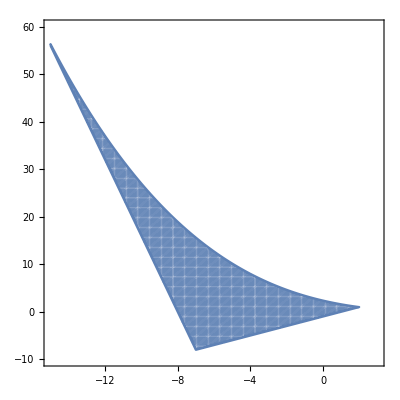

```mathematica
plotIntersection=RegionPlot[(-16<alpha≤-7&&-64-8 alpha<beta<1/216 (512-192 alpha+24 alpha^2-alpha^3))||(-7<alpha<2&&-1+alpha<beta<1/216 (512-192 alpha+24 alpha^2-alpha^3)),{alpha,-15,3},{beta,-10,60},Frame->True,Axes->False,AspectRatio->1,PlotPoints->300]
```

```mathematica
(*plot region spanned by parameters, vs. smalles stability region to show that in the healthy case, the equilibrium is always asymptotically stable*)
Show[plotIntersection,p1,AspectRatio->1,PlotLabel->"Strong Gamma SD - healthy state parameters",LabelStyle->Directive[Bold,Black, FontSize->12],FrameLabel->{"α","β"}]
```

-Graphics-

```mathematica
Quit[];
```

```mathematica
(*DISEASED state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*tau_s=tau_g*);
```

```mathematica
(*coefficients and function in rescaled system*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*Determine critical tau using Theorem 2.8*)
Wgs=.;Wsg=.;
rho[w_]:=4/(4+w^2);
theta[w_]:=2*ArcTan[w/2];
w[tau_]:=2 √(1+tau);
mu[tau_]:=-(2+tau)^2/tau
tau[Wgs_,Wsg_]:=If[Length[NSolve[{beta[Wgs,Wsg]==x*(alpha[Wgs,Wsg]-x),x<-1},x]]==0,
Sort[tau/.NSolve[beta[Wgs,Wsg]==((-8+(-4+alpha[Wgs,Wsg]) tau)^2 (-2 alpha[Wgs,Wsg]+(2+tau)^2))/(4 tau (4+tau)^3)&&tau>0,tau]][[1]],
tau/.NSolve[{beta[Wgs,Wsg]==mu[tau]*(alpha[Wgs,Wsg]-mu[tau]),tau>0},tau][[1]]]
```

```mathematica
(*diseased*)
Wgs=10.7;
Wsg=20;
tau[Wgs,Wsg]
```

0.283222

```mathematica
Wsg=.;Wgs=.;
```

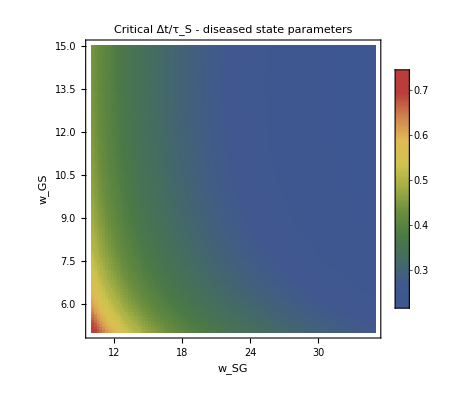

```mathematica
(*around diseased state parameters*)
DensityPlot[tau[Wgs,Wsg],{Wsg,10,35},{Wgs,5,15},PlotLegends->Automatic,PlotPoints->100,ColorFunction->"DarkRainbow",PlotRange->{0,1},FrameLabel->{"w_SG","w_GS"},MeshFunctions->{#3&},Mesh->{{0.2,0.3,0.4,0.5,0.6}},PlotLabel->"Critical Δt/τ_S - diseased state parameters",LabelStyle->Directive[Bold,Black, FontSize->12]]
```